### Simulating the metrology of quantum coherence

Jonas Glatthard (Nottingham), Jesús Rubio (Surrey), and Luis A. Correa (La Laguna)
Contact: j.rubiojimenez@surrey.ac.uk

This code builds on a foundation first developed by Luis A. Correa in 2020.

Last update: July 2025

### Setup

```mathematica
options={MaxRecursion->100,AccuracyGoal->∞,WorkingPrecision->10};
```

```mathematica
markers = {{-Graphics-, 0.03}, {-Graphics-, 0.03}, {-Graphics-, 0.04}, {-Graphics-, 0.03}};
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

### Measurement model

```mathematica
qubitProbability[θ_,λ_]:=ProbabilityDistribution[(x+ (-1)^x θ) (1-λ)+λ/2,{x,0,1,1}]
```

### Construct estimate from dataset

```mathematica
estimateWeight[data_,λ_,θmin_,θmax_]:=Module[
{tpθr={},test={},terror={},cont},
AppendTo[tpθr,1/(θ(1-θ))(PDF[qubitProbability[θ,λ],x]/.x->data⟦1⟧)/NIntegrate[1/(θ(1-θ))(PDF[qubitProbability[θ,λ],x]/.x->data⟦1⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test, Tanh[NIntegrate[tpθr⟦1⟧2ArcTanh[2θ-1],{θ,θmin,θmax},Evaluate@options]/2]/2+1/2];
AppendTo[terror,test⟦1⟧(1-test⟦1⟧)√NIntegrate[tpθr⟦1⟧(2ArcTanh[2test⟦1⟧-1]-2ArcTanh[2 θ-1])^2,{θ,θmin,θmax},Evaluate@options]];
cont=0;
Monitor[Do[cont++;
AppendTo[tpθr,tpθr⟦k-1⟧(PDF[qubitProbability[θ,λ],x]/.x->data⟦k⟧)/NIntegrate[tpθr⟦k-1⟧(PDF[qubitProbability[θ,λ],x]/.x->data⟦k⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test,Tanh[NIntegrate[tpθr⟦k⟧2ArcTanh[2θ-1],{θ,θmin,θmax},Evaluate@options]/2]/2+1/2];
AppendTo[terror,test⟦k⟧(1-test⟦k⟧)√NIntegrate[tpθr⟦k⟧(2ArcTanh[2test⟦k⟧-1]-2ArcTanh[2 θ-1])^2,{θ,θmin,θmax},Evaluate@options]];
,{k,2,Length[data]}],{100N[cont/Length[data]],ProgressIndicator[cont,{2,Length[data]}]}];
Return[Table[Around[test⟦i⟧,terror⟦i⟧],{i,Length[data]}]] 
]//Quiet
```

```mathematica
estimateMetric[data_,λ_,θmin_,θmax_]:=Module[
{tpθr={},test={},terror={},cont},
AppendTo[tpθr,√(1/(θ(1-θ)))(PDF[qubitProbability[θ,λ],x]/.x->data⟦1⟧)/NIntegrate[√(1/(θ(1-θ)))(PDF[qubitProbability[θ,λ],x]/.x->data⟦1⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test,Tan[NIntegrate[-tpθr⟦1⟧2 (1-λ) ArcTan[√(θ/(1-θ))],{θ,θmin,θmax},Evaluate@options]/(2 (-1+λ))]^2/(1+Tan[NIntegrate[-tpθr⟦1⟧2 (1-λ) ArcTan[√(θ/(1-θ))],{θ,θmin,θmax},Evaluate@options]/(2 (-1+λ))]^2)];
AppendTo[terror,(Sqrt[test⟦1⟧(1-test⟦1⟧)]/(1-λ))√NIntegrate[tpθr⟦1⟧(2 (1-λ) ArcTan[√(test⟦1⟧/(1-test⟦1⟧))]-2 (1-λ) ArcTan[√(θ/(1-θ))])^2,{θ,θmin,θmax},Evaluate@options]];
cont=0;
Monitor[Do[cont++;
AppendTo[tpθr,tpθr⟦k-1⟧(PDF[qubitProbability[θ,λ],x]/.x->data⟦k⟧)/NIntegrate[tpθr⟦k-1⟧(PDF[qubitProbability[θ,λ],x]/.x->data⟦k⟧),{θ,θmin,θmax},Evaluate@options]];
AppendTo[test,Tan[NIntegrate[-tpθr⟦k⟧2 (1-λ) ArcTan[√(θ/(1-θ))],{θ,θmin,θmax},Evaluate@options]/(2 (1-λ))]^2/(1+Tan[NIntegrate[-tpθr⟦k⟧2 (1-λ) ArcTan[√(θ/(1-θ))],{θ,θmin,θmax},Evaluate@options]/(2 (1-λ))]^2)];
AppendTo[terror,(Sqrt[test⟦k⟧(1-test⟦k⟧)]/(1-λ))√NIntegrate[tpθr⟦k⟧(2 (1-λ) ArcTan[√(test⟦k⟧/(1-test⟦k⟧))]-2 (1-λ) ArcTan[√(θ/(1-θ))])^2,{θ,θmin,θmax},Evaluate@options]];
,{k,2,Length[data]}],{100N[cont/Length[data]],ProgressIndicator[cont,{2,Length[data]}]}];
Return[Table[Around[test⟦i⟧,terror⟦i⟧],{i,Length[data]}]] 
]//Quiet
```

### Coherence estimation: large sample

Superposition coefficient estimates

```mathematica
a=10^(-5);θmin=a;θmax=1-a;θtrue=0.2;λsim=0.1;μ=120;θest1={};θest2={};
Do[{data=RandomVariate[qubitProbability[θtrue,λsim],μ],θestimates1=estimateWeight[data,λsim,θmin,θmax],AppendTo[θest1,θestimates1[[μ]]],θestimates2=estimateMetric[data,λsim,θmin,θmax],AppendTo[θest2,θestimates2[[μ]]]},{i,1,10}]
```

Coherence estimates

```mathematica
coefficientEstimates1=θestimates1[[All,1]];coefficientErrors1=θestimates1[[All,2]];
coherenceEstimates1=2(1-λsim)Sqrt[coefficientEstimates1(1-coefficientEstimates1)];
coherenceErrors1=coefficientErrors1(1-λsim)Abs[1-2coherenceEstimates1]/Sqrt[(1-coherenceEstimates1)coherenceEstimates1];
cEstimates1=MapThread[Around,{coherenceEstimates1,coherenceErrors1}];

coefficientEstimates2=θestimates2[[All,1]];coefficientErrors2=θestimates2[[All,2]];
coherenceEstimates2=2(1-λsim)Sqrt[coefficientEstimates2(1-coefficientEstimates2)];
coherenceErrors2=coefficientErrors2(1-λsim)Abs[1-2coherenceEstimates2]/Sqrt[(1-coherenceEstimates2)coherenceEstimates2];
cEstimates2=MapThread[Around,{coherenceEstimates2,coherenceErrors2}];

coefficientEst1=θest1[[All,1]];coefficientErr1=θest1[[All,2]];
coherenceEst1=2(1-λsim)Sqrt[coefficientEst1(1-coefficientEst1)];
coherenceErr1=coefficientErr1(1-λsim)Abs[1-2coherenceEst1]/Sqrt[(1-coherenceEst1)coherenceEst1];
cEst1=MapThread[Around,{coherenceEst1,coherenceErr1}];

coefficientEst2=θest2[[All,1]];coefficientErr2=θest2[[All,2]];
coherenceEst2=2(1-λsim)Sqrt[coefficientEst2(1-coefficientEst2)];
coherenceErr2=coefficientErr2(1-λsim)Abs[1-2coherenceEst2]/Sqrt[(1-coherenceEst2)coherenceEst2];
cEst2=MapThread[Around,{coherenceEst2,coherenceErr2}];

ctrue=2(1-λsim)Sqrt[θtrue(1-θtrue)];
```

Save data

```mathematica
(*Export["cEstimates1.txt",cEstimates1];
Export["cEstimates2.txt",cEstimates2];
Export["cEst1.txt",cEst1];
Export["cEst2.txt",cEst2];*)
```

Import published estimates

```mathematica
θtrue=0.2;λsim=0.1;ctrue=2(1-λsim)Sqrt[θtrue(1-θtrue)];
```

```mathematica
μ=120;
cEstimates1=ToExpression/@StringSplit[Import["cEstimates1.txt","Text"],"\n"];
cEstimates2=ToExpression/@StringSplit[Import["cEstimates2.txt","Text"],"\n"];
cEst1=ToExpression/@StringSplit[Import["cEst1.txt","Text"],"\n"];
cEst2=ToExpression/@StringSplit[Import["cEst2.txt","Text"],"\n"];
```

Variability

```mathematica
nsr1=Round[100Mean[(cEst1[[All,1]]-Mean[cEst1[[All,1]]])^2]/Mean[cEst1[[All,1]]]^2,0.01]
nsr2=Round[100Mean[(cEst2[[All,1]]-Mean[cEst2[[All,1]]])^2]/Mean[cEst2[[All,1]]]^2,0.01]
```

0.38

0.34

Plots

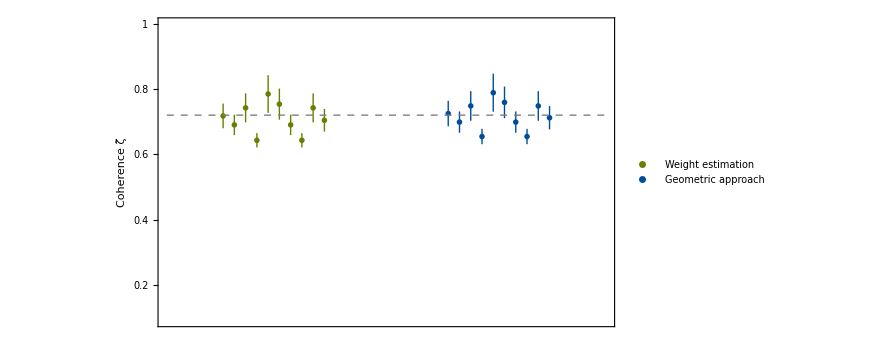

```mathematica
scatter1=Show[ListLinePlot[cEstimates1⟦1;;μ⟧,PlotRange->All,PlotStyle->{RGBColor[0.4,0.5,0],Thick}, PlotMarkers->None,IntervalMarkers->"None",Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->Directive["Times",21,Black],FrameLabel->{"Repetitions μ"},AspectRatio->0.45],ListLinePlot[cEstimates1⟦1;;μ⟧,PlotRange->All,PlotStyle->{RGBColor[0.4,0.5,0]}, PlotMarkers->None,IntervalMarkers->"Bands"],Plot[ctrue,{x,0,μ},PlotStyle->{Gray,Dashed, Thick}],PlotRange->{{1,μ-1},{0.1,1}},ImageSize->275,Epilog-> Inset[Style["(a)",21],Offset[{-3,-3},Scaled[{1,1}]],{Right,Top}]];
scatter2=Show[ListLinePlot[cEstimates2⟦1;;μ⟧,PlotRange->All,PlotStyle-> {RGBColor[0,0.3,0.6],Thick},PlotMarkers->None,IntervalMarkers->"None",Frame->True,Axes->False,FrameTicks->{{Automatic,None},{Automatic,None}},LabelStyle->Directive["Times",21,Black],FrameLabel->{"Repetitions μ"},AspectRatio->0.45],ListLinePlot[cEstimates2⟦1;;μ⟧,PlotRange->All,PlotStyle-> {RGBColor[0,0.3,0.6]},PlotMarkers->None,IntervalMarkers->"Bands"],Plot[ctrue,{x,0,μ},PlotStyle->{Gray,Dashed,Thick}],PlotRange->{{1,μ-1},{0.1,1}},ImageSize->275,Epilog-> Inset[Style["(b)",21],Offset[{-3,-3},Scaled[{1,1}]],{Right,Top}]];
Show[ListPlot[{Partition[Riffle[5+#&/@Range[-2,3,0.5],cEst1],2],Partition[Riffle[15+#&/@Range[-2,3,0.5],cEst2],2]},FrameStyle->Directive["Times",24,Black],PlotStyle->{RGBColor[0.4,0.5,0],RGBColor[0,0.3,0.6]},PlotMarkers->{"OpenMarkers",8},PlotLegends->Placed[LineLegend[{"Weight estimation", "Geometric approach"},LegendLayout->{"Row",1},LabelStyle->Directive["Times",21,Black]],{0.5,0.92}]],Plot[ctrue,{x,0.5,20},PlotStyle->{Gray,Dashed,Thick}],ImageSize->650,Epilog->{Inset[scatter1,ImageScaled[{0.34,0.29}]],Inset[scatter2,ImageScaled[{0.78,0.29}]]},Frame->True,Axes->False,FrameTicks->{{{{0,"0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1"}},{{0,""},{.2,""},{.4,""},{.6,""},{.8,""},{1,""}}},{None,None}},AspectRatio->0.55,FrameLabel->{None,"Coherence ζ̃"},PlotRange->{0.09,1}]
```

### Coherence estimation: small sample

Superposition coefficient estimates

```mathematica
a=10^(-5);θmin=a;θmax=1-a;θtrue=0.2;λsim=0.1;μ=20;θest1={};θest2={};
Do[{data=RandomVariate[qubitProbability[θtrue,λsim],μ],θestimates1=estimateWeight[data,λsim,θmin,θmax],AppendTo[θest1,θestimates1[[μ]]],θestimates2=estimateMetric[data,λsim,θmin,θmax],AppendTo[θest2,θestimates2[[μ]]]},{i,1,10}]
```

Coherence estimates

```mathematica
coefficientEst1=θest1[[All,1]];coefficientErr1=θest1[[All,2]];
coherenceEst1=2(1-λsim)Sqrt[coefficientEst1(1-coefficientEst1)];
coherenceErr1=coefficientErr1(1-λsim)Abs[1-2coherenceEst1]/Sqrt[(1-coherenceEst1)coherenceEst1];
cEst1=MapThread[Around,{coherenceEst1,coherenceErr1}];

coefficientEst2=θest2[[All,1]];coefficientErr2=θest2[[All,2]];
coherenceEst2=2(1-λsim)Sqrt[coefficientEst2(1-coefficientEst2)];
coherenceErr2=coefficientErr2(1-λsim)Abs[1-2coherenceEst2]/Sqrt[(1-coherenceEst2)coherenceEst2];
cEst2=MapThread[Around,{coherenceEst2,coherenceErr2}];

ctrue=2(1-λsim)Sqrt[θtrue(1-θtrue)];
```

Save data

```mathematica
(*Export["cEstimates1small.txt",cEstimates1];
Export["cEstimates2small.txt",cEstimates2];
Export["cEst1small.txt",cEst1];
Export["cEst2small.txt",cEst2];*)
```

Import published estimates

```mathematica
cEstimates1=ToExpression/@StringSplit[Import["cEstimates1small.txt","Text"],"\n"];
cEstimates2=ToExpression/@StringSplit[Import["cEstimates2small.txt","Text"],"\n"];
cEst1=ToExpression/@StringSplit[Import["cEst1small.txt","Text"],"\n"];
cEst2=ToExpression/@StringSplit[Import["cEst2small.txt","Text"],"\n"];
```

Variability

```mathematica
nsr1=Round[100Mean[(cEst1[[All,1]]-Mean[cEst1[[All,1]]])^2]/Mean[cEst1[[All,1]]]^2,0.01]
nsr2=Round[100Mean[(cEst2[[All,1]]-Mean[cEst2[[All,1]]])^2]/Mean[cEst2[[All,1]]]^2,0.01]
```

7.08

0.66

Plots

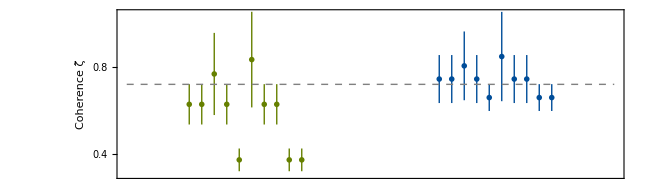

```mathematica
μ=20;
Show[ListPlot[{Partition[Riffle[5+#&/@Range[-2,3,0.5],cEst1],2],Partition[Riffle[15+#&/@Range[-2,3,0.5],cEst2],2]},PlotStyle->{RGBColor[0.4,0.5,0],RGBColor[0,0.3,0.6]},PlotMarkers->{"OpenMarkers",8}],Plot[ctrue,{x,0.5,20},PlotStyle->{Gray,Dashed,Thick}],ImageSize->650,PlotRange->{0.3,1.05},AspectRatio->0.3,FrameStyle->Directive["Times",24,Black],FrameLabel->{None,"Coherence ζ̃"},Frame->True,Axes->False,FrameTicks->{{{{0,"0"},{.2,"0.2"},{.4,"0.4"},{.6,"0.6"},{.8,"0.8"},{1,"1"}},{{0,""},{.2,""},{.4,""},{.6,""},{.8,""},{1,""}}},{None,None}}]
```